```mathematica
(*Columbic interaction of charge*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Assumptions->{Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}
```

Assumptions→{Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}

```mathematica
rhoA[r_]:=A Exp[- α r]
rhoA[r]
```

A ⅇ^(-r α)

```mathematica
rhoB[r_]:=B Exp[-β r]
rhoB[r]
```

B ⅇ^(-r β)

```mathematica
phiA[r_]:=1/(ϵ)((1/r )Integrate[rhoA[x] x^2,{x,0,r}]+Integrate[x rhoA[x],{x,r,Infinity},Assumptions->{Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}])
```

```mathematica
phiA[r]//Expand
```

(2 A)/(r α^3 ϵ)-(2 A ⅇ^(-r α))/(r α^3 ϵ)-(A ⅇ^(-r α))/(α^2 ϵ)

```mathematica
V1=(4 Pi A B/(α^3 *ϵ)(Integrate[r^2 Exp[-β r]*Integrate[1/Sqrt[r^2+R^2-2r R x],{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]<=Re[R]}]+Integrate[r^2 Exp[-β r]*Integrate[1/Sqrt[r^2+R^2-2r R x],{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]>Re[R]}]))//Simplify
```

(8 A B ⅇ^(-R β) π (-2+2 ⅇ^(R β)-R β))/(R α^3 β^3 ϵ)

```mathematica
V1E=V1/.{B->A,β->α}
```

(8 A^2 ⅇ^(-R α) π (-2+2 ⅇ^(R α)-R α))/(R α^6 ϵ)

```mathematica
V2=-4 Pi A B/(α^3*ϵ) (Integrate[r Exp[-α r]*Integrate[Exp[-β Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r Exp[-α r]*Integrate[Exp[-β Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]>Re[R]}])
```

-(4 A B π (-(ⅇ^(-R (α+2 β)) (α-ⅇ^(2 R β) α+2 β-2 ⅇ^(2 R β) β+2 R α β+2 R β^2))/(R β^2 (α+β)^2)-(ⅇ^(-R (α+2 β)) (-α^3+ⅇ^(2 R β) α^3-2 R α^3 β+3 α β^2-3 ⅇ^(2 R β) α β^2+2 R α^2 β^2-2 ⅇ^(R (α+β)) R α^2 β^2-2 β^3-2 ⅇ^(2 R β) β^3+4 ⅇ^(R (α+β)) β^3+2 R α β^3-2 R β^4+2 ⅇ^(R (α+β)) R β^4))/(R β^2 (-α^2+β^2)^2)))/(α^3 ϵ)

```mathematica
V2//Simplify
```

-(8 A B ⅇ^(-R (α+2 β)) π (2 ⅇ^(2 R β) β+ⅇ^(R (α+β)) (-2 β+R (α^2-β^2))))/(R α^3 (α-β)^2 (α+β)^2 ϵ)

```mathematica
V2E=-4 Pi A ^2/(α^3*ϵ) (Integrate[r Exp[-α r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r Exp[-α r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]>Re[R]}])
```

-(4 A^2 π ((ⅇ^(-3 R α) (-3+3 ⅇ^(2 R α)-4 R α))/(4 R α^3)+(ⅇ^(-3 R α) (3-3 ⅇ^(2 R α)+4 R α+2 ⅇ^(2 R α) R α+2 ⅇ^(2 R α) R^2 α^2))/(4 R α^3)))/(α^3 ϵ)

```mathematica
V2E//Simplify
```

-(2 A^2 ⅇ^(-R α) π (1+R α))/(α^5 ϵ)

```mathematica
V3=-2Pi A B/(α^2 ϵ) (Integrate[r^2 Exp[-β r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r^2 Exp[-β r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]>Re[R]}])
```

-1/(α^2 ϵ)2 A B π (-(ⅇ^(-R (2 α+β)) (3 α-3 ⅇ^(2 R α) α+4 R α^2-2 ⅇ^(2 R α) R α^2+2 R^2 α^3+β-ⅇ^(2 R α) β+5 R α β-3 ⅇ^(2 R α) R α β+4 R^2 α^2 β+R β^2-ⅇ^(2 R α) R β^2+2 R^2 α β^2))/(R α^2 (α+β)^3)+1/(R α^2 (α-β)^3 (α+β)^3)ⅇ^(-R (2 α+β)) (3 α^4-3 ⅇ^(2 R α) α^4+4 R α^5+2 ⅇ^(2 R α) R α^5+2 R^2 α^6-8 α^3 β-8 ⅇ^(2 R α) α^3 β+16 ⅇ^(R (α+β)) α^3 β-7 R α^4 β+3 ⅇ^(2 R α) R α^4 β+4 ⅇ^(R (α+β)) R α^4 β-2 R^2 α^5 β+6 α^2 β^2-6 ⅇ^(2 R α) α^2 β^2-2 R α^3 β^2-2 ⅇ^(2 R α) R α^3 β^2-4 R^2 α^4 β^2+8 R α^2 β^3-4 ⅇ^(2 R α) R α^2 β^3-4 ⅇ^(R (α+β)) R α^2 β^3+4 R^2 α^3 β^3-β^4+ⅇ^(2 R α) β^4-2 R α β^4+2 R^2 α^2 β^4-R β^5+ⅇ^(2 R α) R β^5-2 R^2 α β^5))

```mathematica
V3//Simplify
```

-(8 A B ⅇ^(-R (2 α+β)) π (ⅇ^(R (α+β)) β (4 α+R α^2-R β^2)+ⅇ^(2 R α) α (-4 β+R (α^2-β^2))))/(R α^2 (α-β)^3 (α+β)^3 ϵ)

```mathematica
V3E=-2Pi A ^2/(α^2*ϵ )(Integrate[r^2 Exp[-α r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r^2 Exp[-α r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]>Re[R]}])
```

-(2 A^2 π ((ⅇ^(-3 R α) (-2+2 ⅇ^(2 R α)-5 R α+3 ⅇ^(2 R α) R α-4 R^2 α^2))/(4 R α^4)+(ⅇ^(-3 R α) (6-6 ⅇ^(2 R α)+15 R α-3 ⅇ^(2 R α) R α+12 R^2 α^2+6 ⅇ^(2 R α) R^2 α^2+2 ⅇ^(2 R α) R^3 α^3))/(12 R α^4)))/(α^2 ϵ)

```mathematica
V3E//Simplify
```

-(A^2 ⅇ^(-R α) π (3+3 R α+R^2 α^2))/(3 α^5 ϵ)

```mathematica
(*Full potential two diff atoms*)
V=V1+V2+V3
```

(8 A B ⅇ^(-R β) π (-2+2 ⅇ^(R β)-R β))/(R α^3 β^3 ϵ)-(4 A B π (-(ⅇ^(-R (α+2 β)) (α-ⅇ^(2 R β) α+2 β-2 ⅇ^(2 R β) β+2 R α β+2 R β^2))/(R β^2 (α+β)^2)-(ⅇ^(-R (α+2 β)) (-α^3+ⅇ^(2 R β) α^3-2 R α^3 β+3 α β^2-3 ⅇ^(2 R β) α β^2+2 R α^2 β^2-2 ⅇ^(R (α+β)) R α^2 β^2-2 β^3-2 ⅇ^(2 R β) β^3+4 ⅇ^(R (α+β)) β^3+2 R α β^3-2 R β^4+2 ⅇ^(R (α+β)) R β^4))/(R β^2 (-α^2+β^2)^2)))/(α^3 ϵ)-1/(α^2 ϵ)2 A B π (-(ⅇ^(-R (2 α+β)) (3 α-3 ⅇ^(2 R α) α+4 R α^2-2 ⅇ^(2 R α) R α^2+2 R^2 α^3+β-ⅇ^(2 R α) β+5 R α β-3 ⅇ^(2 R α) R α β+4 R^2 α^2 β+R β^2-ⅇ^(2 R α) R β^2+2 R^2 α β^2))/(R α^2 (α+β)^3)+1/(R α^2 (α-β)^3 (α+β)^3)ⅇ^(-R (2 α+β)) (3 α^4-3 ⅇ^(2 R α) α^4+4 R α^5+2 ⅇ^(2 R α) R α^5+2 R^2 α^6-8 α^3 β-8 ⅇ^(2 R α) α^3 β+16 ⅇ^(R (α+β)) α^3 β-7 R α^4 β+3 ⅇ^(2 R α) R α^4 β+4 ⅇ^(R (α+β)) R α^4 β-2 R^2 α^5 β+6 α^2 β^2-6 ⅇ^(2 R α) α^2 β^2-2 R α^3 β^2-2 ⅇ^(2 R α) R α^3 β^2-4 R^2 α^4 β^2+8 R α^2 β^3-4 ⅇ^(2 R α) R α^2 β^3-4 ⅇ^(R (α+β)) R α^2 β^3+4 R^2 α^3 β^3-β^4+ⅇ^(2 R α) β^4-2 R α β^4+2 R^2 α^2 β^4-R β^5+ⅇ^(2 R α) R β^5-2 R^2 α β^5))

```mathematica
V=V//Simplify
```

(8 A B ⅇ^(-R (α+β)) π (2 ⅇ^(R (α+β)) (α^2-β^2)^3+ⅇ^(R β) β^4 (-6 α^2-R α^3+2 β^2+R α β^2)-ⅇ^(R α) α^4 (α^2 (2+R β)-β^2 (6+R β))))/(R α^3 (α-β)^3 β^3 (α+β)^3 ϵ)

```mathematica
(*Full potential of smame atoms*)
```

```mathematica
VE=V1E+V2E+V3E
```

(8 A^2 ⅇ^(-R α) π (-2+2 ⅇ^(R α)-R α))/(R α^6 ϵ)-(4 A^2 π ((ⅇ^(-3 R α) (-3+3 ⅇ^(2 R α)-4 R α))/(4 R α^3)+(ⅇ^(-3 R α) (3-3 ⅇ^(2 R α)+4 R α+2 ⅇ^(2 R α) R α+2 ⅇ^(2 R α) R^2 α^2))/(4 R α^3)))/(α^3 ϵ)-(2 A^2 π ((ⅇ^(-3 R α) (-2+2 ⅇ^(2 R α)-5 R α+3 ⅇ^(2 R α) R α-4 R^2 α^2))/(4 R α^4)+(ⅇ^(-3 R α) (6-6 ⅇ^(2 R α)+15 R α-3 ⅇ^(2 R α) R α+12 R^2 α^2+6 ⅇ^(2 R α) R^2 α^2+2 ⅇ^(2 R α) R^3 α^3))/(12 R α^4)))/(α^2 ϵ)

```mathematica
VE=VE//Simplify
```

(A^2 ⅇ^(-R α) π (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(3 R α^6 ϵ)

```mathematica
ExtraV1=-2/(4*Pi*ϵ Rc)*(16 Pi^2)Integrate[r^2rhoA[r],{r,0,Infinity},Assumptions->Re[α]>0] Integrate[r^2 rhoB[r],{r,0,Infinity},Assumptions->Re[β]>0]
```

-(32 A B π)/(Rc α^3 β^3 ϵ)

```mathematica
ExtraV1E=Limit[ExtraV1,β->α]
```

-(32 A B π)/(Rc α^6 ϵ)

```mathematica
ExtraPhi=A/(2 ϵ Rc^2)(Integrate[r^2 Exp[-α r]*Integrate[Sqrt[r^2+R^2-2r R x],{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Re[α]>0,Re[r]<Re[R]}]+Integrate[r^2 Exp[-α r]*Integrate[Sqrt[r^2+R^2-2r R x],{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Re[α]>0,Re[r]>Re[R]}])
```

(A ((4 ⅇ^(-R α) (3+2 R α) (3+R α+R^2 α^2))/(3 α^4)+(4 ⅇ^(-R α) (-12+12 ⅇ^(R α)-12 R α-9 R^2 α^2+3 ⅇ^(R α) R^2 α^2-5 R^3 α^3-2 R^4 α^4))/(3 R α^5)))/(2 Rc^2 ϵ)

```mathematica
ExtraPhiExpand=ExtraPhi/.{R->r}//Expand
```

(8 A)/(r Rc^2 α^5 ϵ)-(8 A ⅇ^(-r α))/(r Rc^2 α^5 ϵ)-(2 A ⅇ^(-r α))/(Rc^2 α^4 ϵ)+(2 A r)/(Rc^2 α^3 ϵ)

```mathematica
ExtraV21=2 Pi(Integrate[r^2 rhoB[r]*Integrate[ExtraPhiExpand[[1]]/.{r->Sqrt[r^2+R^2-2r R x]},{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Re[α]>0,Im[β]==0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r^2 rhoB[r]*Integrate[ExtraPhiExpand[[1]]/.{r->Sqrt[r^2+R^2-2r R x]},{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Re[α]>0,Re[r]>Re[R],Im[β]==0,Re[β]>0}])
```

2 π ((16 A B ⅇ^(-R β) (1+R β))/(Rc^2 α^5 β^2 ϵ)+(16 A B ⅇ^(-R β) (-2+2 ⅇ^(R β)-2 R β-R^2 β^2))/(R Rc^2 α^5 β^3 ϵ))

```mathematica
ExtraV21//Simplify
```

(32 A B ⅇ^(-R β) π (-2+2 ⅇ^(R β)-R β))/(R Rc^2 α^5 β^3 ϵ)

```mathematica
ExtraV23=2 Pi(Integrate[r^2 rhoB[r]*Integrate[ExtraPhiExpand[[3]]/.{r->Sqrt[r^2+R^2-2r R x]},{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Re[α]>0,Im[β]==0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r^2 rhoB[r]*Integrate[ExtraPhiExpand[[3]]/.{r->Sqrt[r^2+R^2-2r R x]},{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Re[α]>0,Re[r]>Re[R],Im[β]==0,Re[β]>0}])
```

2 π ((2 A B ⅇ^(-R (2 α+β)) (3 α-3 ⅇ^(2 R α) α+4 R α^2-2 ⅇ^(2 R α) R α^2+2 R^2 α^3+β-ⅇ^(2 R α) β+5 R α β-3 ⅇ^(2 R α) R α β+4 R^2 α^2 β+R β^2-ⅇ^(2 R α) R β^2+2 R^2 α β^2))/(R Rc^2 α^6 (α+β)^3 ϵ)-1/(R Rc^2 α^6 (α-β)^3 (α+β)^3 ϵ)2 A B ⅇ^(-R (2 α+β)) (3 α^4-3 ⅇ^(2 R α) α^4+4 R α^5+2 ⅇ^(2 R α) R α^5+2 R^2 α^6-8 α^3 β-8 ⅇ^(2 R α) α^3 β+16 ⅇ^(R (α+β)) α^3 β-7 R α^4 β+3 ⅇ^(2 R α) R α^4 β+4 ⅇ^(R (α+β)) R α^4 β-2 R^2 α^5 β+6 α^2 β^2-6 ⅇ^(2 R α) α^2 β^2-2 R α^3 β^2-2 ⅇ^(2 R α) R α^3 β^2-4 R^2 α^4 β^2+8 R α^2 β^3-4 ⅇ^(2 R α) R α^2 β^3-4 ⅇ^(R (α+β)) R α^2 β^3+4 R^2 α^3 β^3-β^4+ⅇ^(2 R α) β^4-2 R α β^4+2 R^2 α^2 β^4-R β^5+ⅇ^(2 R α) R β^5-2 R^2 α β^5))

```mathematica
ExtraV23//Simplify
```

-(16 A B ⅇ^(-R (2 α+β)) π (ⅇ^(R (α+β)) β (4 α+R α^2-R β^2)+ⅇ^(2 R α) α (-4 β+R (α^2-β^2))))/(R Rc^2 α^4 (α-β)^3 (α+β)^3 ϵ)

```mathematica
ExtraV24=2 Pi(Integrate[r^2 rhoB[r]*Integrate[ExtraPhiExpand[[4]]/.{r->Sqrt[r^2+R^2-2r R x]},{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Re[α]>0,Im[β]==0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r^2 rhoB[r]*Integrate[ExtraPhiExpand[[4]]/.{r->Sqrt[r^2+R^2-2r R x]},{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Re[α]>0,Re[r]>Re[R],Im[β]==0,Re[β]>0}])
```

2 π ((8 A B ⅇ^(-R β) (3+2 R β) (3+R β+R^2 β^2))/(3 Rc^2 α^3 β^4 ϵ)+(8 A B ⅇ^(-R β) (-12+12 ⅇ^(R β)-12 R β-9 R^2 β^2+3 ⅇ^(R β) R^2 β^2-5 R^3 β^3-2 R^4 β^4))/(3 R Rc^2 α^3 β^5 ϵ))

```mathematica
ExtraV24//Simplify
```

(16 A B ⅇ^(-R β) π (-4-R β+ⅇ^(R β) (4+R^2 β^2)))/(R Rc^2 α^3 β^5 ϵ)

```mathematica
ExtraV22=2 Pi(Integrate[r^2 ExtraPhiExpand[[2]]*Integrate[rhoB[r]/.{r->Sqrt[r^2+R^2-2r R x]},{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Re[α]>0,Im[β]==0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r^2 ExtraPhiExpand[[2]]*Integrate[rhoB[r]/.{r->Sqrt[r^2+R^2-2r R x]},{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Re[α]>0,Re[r]>Re[R],Im[β]==0,Re[β]>0}])
```

2 π ((8 A B ⅇ^(-R (α+2 β)) (α-ⅇ^(2 R β) α+2 β-2 ⅇ^(2 R β) β+2 R α β+2 R β^2))/(R Rc^2 α^5 β^2 (α+β)^2 ϵ)-(8 A B ⅇ^(-R (α+2 β)) (α^3-ⅇ^(2 R β) α^3+2 R α^3 β-3 α β^2+3 ⅇ^(2 R β) α β^2-2 R α^2 β^2+2 ⅇ^(R (α+β)) R α^2 β^2+2 β^3+2 ⅇ^(2 R β) β^3-4 ⅇ^(R (α+β)) β^3-2 R α β^3+2 R β^4-2 ⅇ^(R (α+β)) R β^4))/(R Rc^2 α^5 β^2 (α^2-β^2)^2 ϵ))

```mathematica
ExtraV22//Simplify
```

-(32 A B ⅇ^(-R (α+2 β)) π (2 ⅇ^(2 R β) β+ⅇ^(R (α+β)) (-2 β+R (α^2-β^2))))/(R Rc^2 α^5 (α-β)^2 (α+β)^2 ϵ)

```mathematica
ExtraV=(ExtraV1+ExtraV21+ExtraV22+ExtraV23+ExtraV24)//Simplify
```

(16 A B ⅇ^(-3 R α-4 R β) π (ⅇ^(2 R (α+2 β)) β^6 (8 α^2+R α^3-4 β^2-R α β^2)+ⅇ^(3 R (α+β)) α^6 (α^2 (4+R β)-β^2 (8+R β))-ⅇ^(3 R α+4 R β) (α^2-β^2)^3 (4 β^2+α^2 (4+R^2 β^2-2 R Rc β^2))))/(R Rc^2 α^5 β^5 (-α+β)^3 (α+β)^3 ϵ)

```mathematica
ExtraVE=Limit[ExtraV,{β->α}]/.{B->A}
```

{(2 A^2 ⅇ^(-R α) π (-192-87 R α-15 R^2 α^2-R^3 α^3+24 ⅇ^(R α) (8+R^2 α^2-2 R Rc α^2)))/(3 R Rc^2 α^8 ϵ)}

```mathematica
TotalVDSF=(V+ExtraV)//Simplify
```

1/(R Rc^2 α^5 (α-β)^3 β^5 (α+β)^3 ϵ)8 A B π (2 ⅇ^(-R α) β^6 (-8 α^2-R α^3+4 β^2+R α β^2)+ⅇ^(-R β) (-2 α^8 (4+R β)+2 α^6 β^2 (8+R β))+2 (α^2-β^2)^3 (4 β^2+α^2 (4+R^2 β^2-2 R Rc β^2))+ⅇ^(-R (α+β)) Rc^2 α^2 β^2 (2 ⅇ^(R (α+β)) (α^2-β^2)^3+ⅇ^(R β) β^4 (-6 α^2-R α^3+2 β^2+R α β^2)-ⅇ^(R α) α^4 (α^2 (2+R β)-β^2 (6+R β))))

```mathematica
TotalVEDSF=(VE+ExtraVE)//Simplify
```

{(A^2 ⅇ^(-R α) π (-R^3 α^3 (2+Rc^2 α^2)-48 (8+Rc^2 α^2)+48 ⅇ^(R α) (8+R^2 α^2-2 R Rc α^2+Rc^2 α^2)-3 R^2 α^2 (10+3 Rc^2 α^2)-3 R α (58+11 Rc^2 α^2)))/(3 R Rc^2 α^8 ϵ)}

```mathematica
TotalVSP=(V+ExtraV1/2)//Simplify
```

-(8 A B ⅇ^(-R (α+β)) π (2 ⅇ^(R (α+β)) (R-Rc) (α^2-β^2)^3-ⅇ^(R β) Rc β^4 (-6 α^2-R α^3+2 β^2+R α β^2)+ⅇ^(R α) Rc α^4 (α^2 (2+R β)-β^2 (6+R β))))/(R Rc α^3 (α-β)^3 β^3 (α+β)^3 ϵ)

```mathematica
TotalVESP=Limit[TotalVSP,{β->α}]/.{B->A}
```

{-(A^2 ⅇ^(-R α) π (48 ⅇ^(R α) (R-Rc)+Rc (48+33 R α+9 R^2 α^2+R^3 α^3)))/(3 R Rc α^6 ϵ)}

```mathematica
fePt=2.336509;
rePt=2.771916;
betaPt=3.78975;
feO=1.39478;
reO=3.64857;
gammaO=2.11725;
APt=fePt*Exp[betaPt];
alphaPt=betaPt/rePt;
AO=feO*Exp[gammaO];
alphaO=gammaO/reO;
```

```mathematica
Rcconst=10;
```

```mathematica
force=-D[{TotalVDSF,V,TotalVSP},R];
forceE=-D[{TotalVEDSF,VE,TotalVESP},R];
```

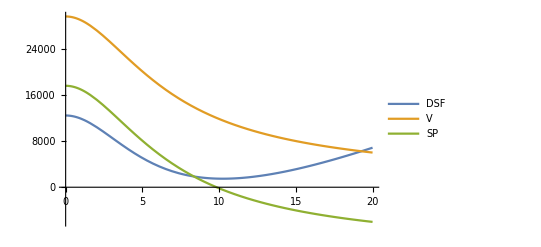

```mathematica
Plot[{TotalVDSF/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO,Rc->Rcconst},V/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO,Rc->Rcconst},TotalVSP/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO,Rc->Rcconst}},{r,0,20},PlotLegends->{"DSF","V","SP"},PlotRange->Full]
```

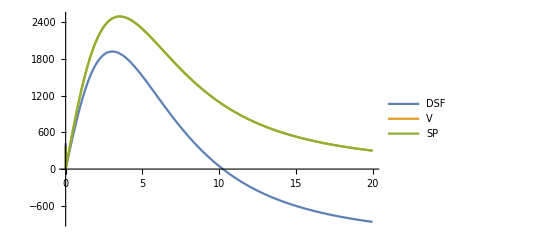

```mathematica
Plot[{force[[1]]/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO,Rc->Rcconst},force[[2]]/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO,Rc->Rcconst},force[[3]]/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO,Rc->Rcconst}},{r,0,20},PlotLegends->{"DSF","V","SP"},PlotRange->Full]
```

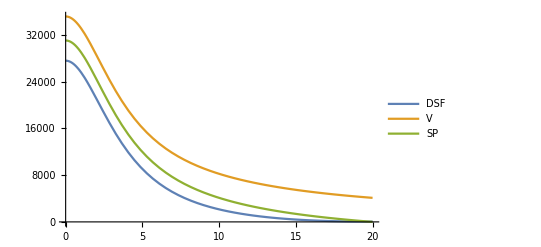

```mathematica
(*same atoms*)Plot[{TotalVEDSF/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO,Rc->Rcconst},VE/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO,Rc->Rcconst},TotalVESP/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO,Rc->Rcconst}},{r,0,20},PlotLegends->{"DSF","V","SP"},PlotRange->Full]
```

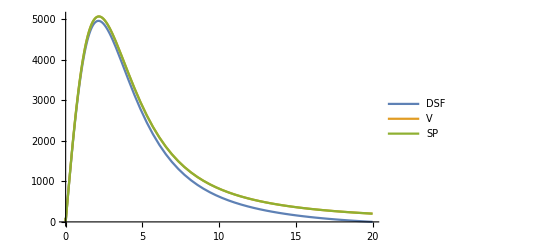

```mathematica
Plot[{forceE[[1]]/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO,Rc->Rcconst},forceE[[2]]/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO,Rc->Rcconst},forceE[[3]]/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO,Rc->Rcconst}},{r,0,20},PlotLegends->{"DSF","V","SP"},PlotRange->Full]
```